```mathematica
σ[z_]:=1/(1+ⅇ^-z)
```

```mathematica
D[σ[z],z]
```

ⅇ^-z/((1+ⅇ^-z)^2)

```mathematica
dσdz[z_]:=ⅇ^-z/((1+ⅇ^-z)^2)
```

```mathematica
D[σ[z],{z,2}]
```

(2 ⅇ^(-2 z))/((1+ⅇ^-z)^3)-ⅇ^-z/((1+ⅇ^-z)^2)

```mathematica
d2σdz2[z_]:=(2 ⅇ^(-2 z))/((1+ⅇ^-z)^3)-ⅇ^-z/((1+ⅇ^-z)^2)
```

```mathematica
D[σ[z],{z,3}]
```

(6 ⅇ^(-3 z))/((1+ⅇ^-z)^4)-(6 ⅇ^(-2 z))/((1+ⅇ^-z)^3)+ⅇ^-z/((1+ⅇ^-z)^2)

```mathematica
d3σdz3[z_]:=(6 ⅇ^(-3 z))/((1+ⅇ^-z)^4)-(6 ⅇ^(-2 z))/((1+ⅇ^-z)^3)+ⅇ^-z/((1+ⅇ^-z)^2)
```

```mathematica
D[σ[z],{z,4}]
```

(24 ⅇ^(-4 z))/((1+ⅇ^-z)^5)-(36 ⅇ^(-3 z))/((1+ⅇ^-z)^4)+(14 ⅇ^(-2 z))/((1+ⅇ^-z)^3)-ⅇ^-z/((1+ⅇ^-z)^2)

```mathematica
d4σdz4[z_]:=(24 ⅇ^(-4 z))/((1+ⅇ^-z)^5)-(36 ⅇ^(-3 z))/((1+ⅇ^-z)^4)+(14 ⅇ^(-2 z))/((1+ⅇ^-z)^3)-ⅇ^-z/((1+ⅇ^-z)^2)
```

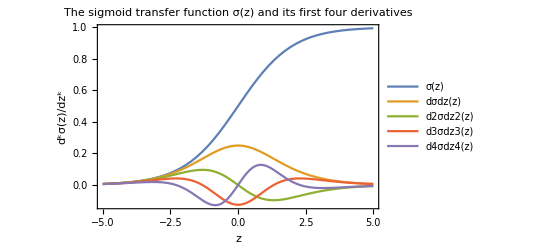

```mathematica
Plot[{σ[z],dσdz[z],d2σdz2[z],d3σdz3[z],d4σdz4[z]},{z,-5,5},PlotRange->Full,AxesLabel->{"z","d^kσ(z)/dz^k"},PlotLegends->"Expressions",PlotLabel->"The sigmoid transfer function σ(z) and its first four derivatives",Frame->True]
```

```mathematica
x=Range[0,1,1/9]
```

{0,1/9,2/9,1/3,4/9,5/9,2/3,7/9,8/9,1}

```mathematica
σ[x]//N
```

{0.5,0.527749,0.555328,0.58257,0.609318,0.635424,0.660756,0.685201,0.708661,0.731059}